```mathematica
G=Graph[{1<->2,1<->3,2<->3,2<->4,3<->4},VertexLabels->"Name",EdgeWeight->{2,2,1,1,1}]
A=Normal[WeightedAdjacencyMatrix[G]]
```

-Graphics-

{{0,2,2,0},{2,0,1,1},{2,1,0,1},{0,1,1,0}}

```mathematica
SetDirectory["~/maths/ibmer/papers/mdgp/intro_dg"]
```

/Users/liberti/maths/ibmer/papers/mdgp/intro_dg

```mathematica
Get["ApproxRealize.m"]
```

```mathematica
x = StochasticProximityEmbedding[G, 2, 20]
```

{{2.23937,-0.705083},{4.20496,-0.573359},{4.07289,-1.55343},{5.00972,-1.12297}}

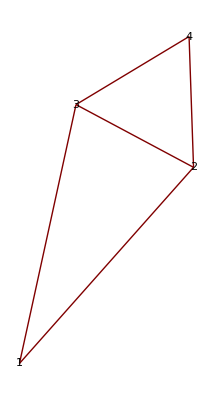

```mathematica
GraphPlot[G, VertexLabeling->True, VertexCoordinateRules->x]
```

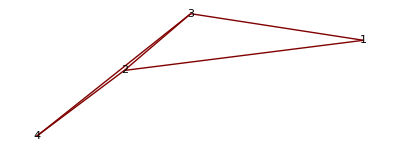
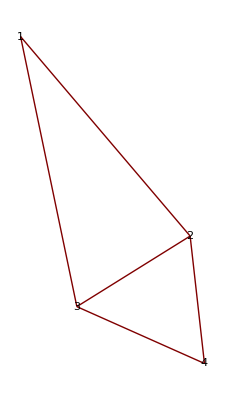
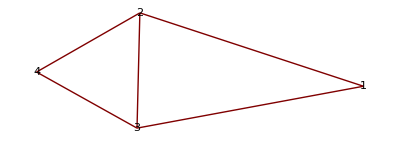
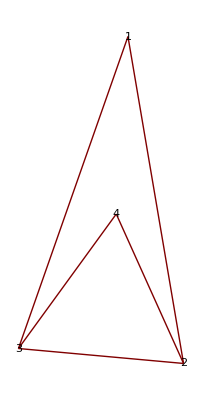
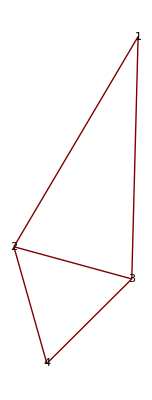
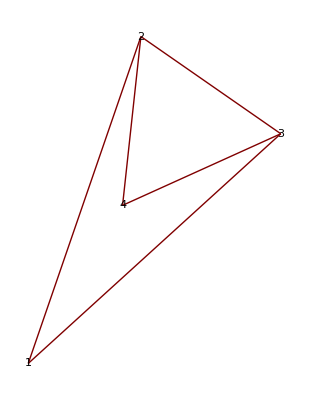
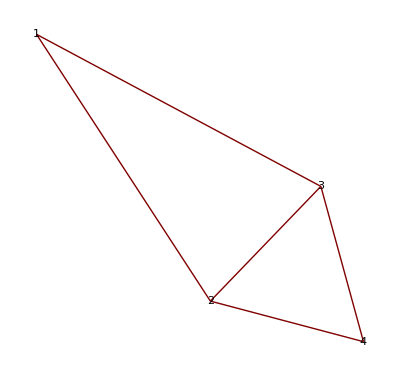
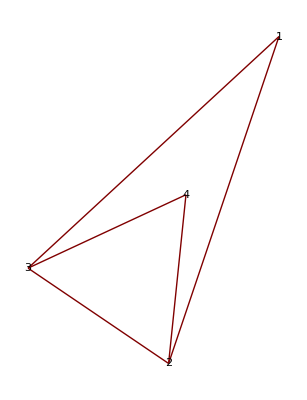

```mathematica
Map[(GraphPlot[G, VertexLabeling->True,VertexCoordinateRules-> StochasticProximityEmbedding[G,2,#]])&, Range[10,100,10]]
```

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
B=DistanceMatrix[x, DistanceFunction->EuclideanDistance]
```

{{0.,2.00725,1.99856,2.81203},{2.00725,0.,0.990755,1.01183},{1.99856,0.990755,0.,0.993219},{2.81203,1.01183,0.993219,0.}}

```mathematica
A=Normal[WeightedAdjacencyMatrix[G]]
```

{{0,2,2,0},{2,0,1,1},{2,1,0,1},{0,1,1,0}}

```mathematica
Abs[A-B]
```

{{0.,0.00725034,0.00143627,2.81203},{0.00725034,0.,0.00924525,0.0118276},{0.00143627,0.00924525,0.,0.00678145},{2.81203,0.0118276,0.00678145,0.}}

```mathematica
EuclideanDistanceMatrix[x]
```

{{0.,2.00725,1.99856,2.81203},{2.00725,0.,0.990755,1.01183},{1.99856,0.990755,0.,0.993219},{2.81203,1.01183,0.993219,0.}}

```mathematica
G1=RandomGraph[{10,30},EdgeWeight->RandomInteger[5,30]]
```

-Graphics-

```mathematica
x = StochasticProximityEmbedding[G1, 3, 10000]
```

{{-10.9066,1.54726,37.3698},{-9.35275,0.3172,36.4531},{-8.64156,1.14353,36.7048},{-10.8505,1.66775,37.0264},{-6.66702,1.21825,37.0326},{-9.07674,1.23821,34.8206},{-10.7263,1.69359,38.2926},{-8.72852,0.957029,33.9548},{-9.91723,0.681007,35.6655},{-8.92942,1.06195,35.4699}}

```mathematica
GraphPlot3D[G1, VertexLabeling->True, VertexCoordinateRules->x]
```

-Graphics3D-

```mathematica
AA = Normal[WeightedAdjacencyMatrix[G1]]
```

{{0,2,1,0,5,4,1,4,0,0},{2,0,1,3,0,3,2,0,0,1},{1,1,0,0,1,4,0,0,0,0},{0,3,0,0,0,2,1,4,1,3},{5,0,1,0,0,3,0,4,4,0},{4,3,4,2,3,0,0,0,1,0},{1,2,0,1,0,0,0,5,5,0},{4,0,0,4,4,0,5,0,2,1},{0,0,0,1,4,1,5,2,0,0},{0,1,0,3,0,0,0,1,0,0}}

```mathematica
AB = EuclideanDistanceMatrix[x]
```

{{0.,2.18352,2.39492,0.368234,4.26567,3.15316,0.951603,4.09323,2.15263,2.7847},{2.18352,0.,1.1189,2.09667,2.8915,1.89464,2.67676,2.65342,1.03505,1.3041},{2.39492,1.1189,0.,2.293,2.00296,1.9361,2.67773,2.75764,1.70918,1.27064},{0.368234,2.09667,2.293,0.,4.2076,2.86295,1.2726,3.80036,1.92268,2.54568},{4.26567,2.8915,2.00296,4.2076,0.,3.2711,4.27689,3.71358,3.56671,2.75409},{3.15316,1.89464,1.9361,2.86295,3.2711,0.,3.87089,0.974615,1.31561,0.688714},{0.951603,2.67676,2.67773,1.2726,4.27689,3.87089,0.,4.83225,2.92947,3.4053},{4.09323,2.65342,2.75764,3.80036,3.71358,0.974615,4.83225,0.,2.10137,1.5319},{2.15263,1.03505,1.70918,1.92268,3.56671,1.31561,2.92947,2.10137,0.,1.07665},{2.7847,1.3041,1.27064,2.54568,2.75409,0.688714,3.4053,1.5319,1.07665,0.}}

```mathematica
y=ApproxRealizeGraph[G1]
```

{{-0.239133,-0.269651,-0.490378,0.757318,-1.6526},{-0.99042,-0.898622,0.0269222,-0.275329,1.06685},{-1.22351,0.508025,0.919984,0.217668,-0.62802},{0.191303,0.240323,0.434813,-1.76475,-0.410956},{1.03954,0.235805,-0.863694,-0.170496,-0.0691427},{-0.0821236,0.332905,-0.0820825,-0.0317221,0.56942},{-0.66214,0.523933,-1.15501,-0.326075,0.345177},{0.831241,-1.30124,0.360462,-0.266247,-0.248744},{0.124258,-0.221545,0.0899718,1.33941,0.579288},{1.01098,0.850063,0.75901,0.520224,0.448721}}

```mathematica
EuclideanDistanceMatrix[y]
```

{{0.,3.11278,2.21447,3.03379,2.32337,2.47273,2.53284,2.43973,2.40652,2.97477},{3.11278,0.,2.43848,2.69487,2.73904,1.63105,2.0129,2.30709,2.13308,2.93504},{2.21447,2.43848,0.,2.50716,2.97322,1.95797,2.42152,2.86121,2.39866,2.52721},{3.03379,2.69487,2.50716,0.,2.25037,2.07727,2.44497,2.25018,3.30956,2.66626},{2.32337,2.73904,2.97322,2.25037,0.,1.51839,1.8054,1.98642,2.15793,1.93819},{2.47273,1.63105,1.95797,2.07727,1.51839,0.,1.2888,2.10354,1.50324,1.57765},{2.53284,2.0129,2.42152,2.44497,1.8054,1.2888,0.,2.86608,2.35644,2.70113},{2.43973,2.30709,2.86121,2.25018,1.98642,2.10354,2.86608,0.,2.23663,2.43397},{2.40652,2.13308,2.39866,3.30956,2.15793,1.50324,2.35644,2.23663,0.,1.75224},{2.97477,2.93504,2.52721,2.66626,1.93819,1.57765,2.70113,2.43397,1.75224,0.}}

```mathematica
Flatten[Table[{i,j}, {i,n}, {j, n}],1]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}

```mathematica
B = Map[(If[AA[[First[#], Last[#]]] > 0, AA[[First[#], Last[#]]], AB[[First[#], Last[#]]]])&, 
	Flatten[Table[{i,j}, {i,n}, {j, n}],1]]
```

{0.,2,1,0.368234,5,4,1,4,2.15263,2.7847,2,0.,1,3,2.8915,3,2,2.65342,1.03505,1,1,1,0.,2.293,1,4,2.67773,2.75764,1.70918,1.27064,0.368234,3,2.293,0.,4.2076,2,1,4,1,3,5,2.8915,1,4.2076,0.,3,4.27689,4,4,2.75409,4,3,4,2,3,0.,3.87089,0.974615,1,0.688714,1,2,2.67773,1,4.27689,3.87089,0.,5,5,3.4053,4,2.65342,2.75764,4,4,0.974615,5,0.,2,1,2.15263,1.03505,1.70918,1,4,1,5,2,0.,1.07665,2.7847,1,1.27064,3,2.75409,0.688714,3.4053,1,1.07665,0.}

```mathematica
n = Length[VertexList[G1]]
```

10

```mathematica
AC =CompletePartialDistanceMatrixBy[AA, AB]
```

{{0.,2,1,0.368234,5,4,1,4,2.15263,2.7847},{2,0.,1,3,2.8915,3,2,2.65342,1.03505,1},{1,1,0.,2.293,1,4,2.67773,2.75764,1.70918,1.27064},{0.368234,3,2.293,0.,4.2076,2,1,4,1,3},{5,2.8915,1,4.2076,0.,3,4.27689,4,4,2.75409},{4,3,4,2,3,0.,3.87089,0.974615,1,0.688714},{1,2,2.67773,1,4.27689,3.87089,0.,5,5,3.4053},{4,2.65342,2.75764,4,4,0.974615,5,0.,2,1},{2.15263,1.03505,1.70918,1,4,1,5,2,0.,1.07665},{2.7847,1,1.27064,3,2.75409,0.688714,3.4053,1,1.07665,0.}}

```mathematica
Dimensions[AB]
```

{10,10}

```mathematica
x =ApproxRealizeCompleteDistanceMatrix[AC]
```

{{-1.19827,-0.58441,0.495354,0.0441874,-0.105899},{-0.130164,0.245149,0.422608,0.400543,0.482142},{-0.238269,0.644775,0.774696,-0.270403,-0.240968},{-0.803452,-0.610602,-0.533142,-0.593436,-0.0836159},{0.667048,1.59623,-0.238362,-0.438943,0.00268685},{0.884127,-0.43827,-1.02801,-0.000320821,0.0552873},{-1.58784,0.411475,-0.594324,0.46578,-0.0110383},{1.24057,-0.420094,0.172473,0.584167,-0.308953},{0.600864,-0.867084,0.454295,-0.559899,0.208872},{0.56538,0.0228299,0.0744081,0.368325,0.00148643}}

```mathematica
AD = EuclideanDistanceMatrix[x]
```

{{0.,1.51891,1.62103,1.27335,3.00302,2.58966,1.58672,2.5322,1.94486,1.94242},{1.51891,0.,1.12624,1.84585,1.95767,1.98571,1.85314,1.74459,1.66421,0.941551},{1.62103,1.12624,0.,1.9326,1.68491,2.41727,2.08442,2.10202,1.83812,1.41061},{1.27335,1.84585,1.9326,0.,2.67408,1.86911,1.67058,2.47987,1.76057,1.89111},{3.00302,1.95767,1.68491,2.67408,0.,2.23719,2.72646,2.38896,2.57084,1.79873},{2.58966,1.98571,2.41727,1.86911,2.23719,0.,2.69117,1.42928,1.67274,1.29164},{1.58672,1.85314,2.08442,1.67058,2.72646,2.69117,0.,3.06303,2.93685,2.29003},{2.5322,1.74459,2.10202,2.47987,2.38896,1.42928,3.06303,0.,1.50515,0.897019},{1.94486,1.66421,1.83812,1.76057,2.57084,1.67274,2.93685,1.50515,0.,1.35725},{1.94242,0.941551,1.41061,1.89111,1.79873,1.29164,2.29003,0.897019,1.35725,0.}}

```mathematica
AA - AD
```

{{0.,0.481088,-0.621031,-1.27335,1.99698,1.41034,-0.586722,1.4678,-1.94486,-1.94242},{0.481088,0.,-0.126237,1.15415,-1.95767,1.01429,0.146864,-1.74459,-1.66421,0.0584491},{-0.621031,-0.126237,0.,-1.9326,-0.68491,1.58273,-2.08442,-2.10202,-1.83812,-1.41061},{-1.27335,1.15415,-1.9326,0.,-2.67408,0.130885,-0.670584,1.52013,-0.760566,1.10889},{1.99698,-1.95767,-0.68491,-2.67408,0.,0.762813,-2.72646,1.61104,1.42916,-1.79873},{1.41034,1.01429,1.58273,0.130885,0.762813,0.,-2.69117,-1.42928,-0.672738,-1.29164},{-0.586722,0.146864,-2.08442,-0.670584,-2.72646,-2.69117,0.,1.93697,2.06315,-2.29003},{1.4678,-1.74459,-2.10202,1.52013,1.61104,-1.42928,1.93697,0.,0.494849,0.102981},{-1.94486,-1.66421,-1.83812,-0.760566,1.42916,-0.672738,2.06315,0.494849,0.,-1.35725},{-1.94242,0.0584491,-1.41061,1.10889,-1.79873,-1.29164,-2.29003,0.102981,-1.35725,0.}}

```mathematica
AA
```

{{0,2,1,0,5,4,1,4,0,0},{2,0,1,3,0,3,2,0,0,1},{1,1,0,0,1,4,0,0,0,0},{0,3,0,0,0,2,1,4,1,3},{5,0,1,0,0,3,0,4,4,0},{4,3,4,2,3,0,0,0,1,0},{1,2,0,1,0,0,0,5,5,0},{4,0,0,4,4,0,5,0,2,1},{0,0,0,1,4,1,5,2,0,0},{0,1,0,3,0,0,0,1,0,0}}

```mathematica
Total[Map[(Abs[AA[[First[#],Last[#]]]-AD[[First[#],Last[#]]]])&,Position[AA, x_ /; x>0]]]
```

49.1927